4858450636189713423582095962494202044581400587983244549483093085061934704708809928450644769865524364849997247024915119110411605739177407856919754326571855442057210445735883681829823754139634338225199452191651284348332905131193199935241375876523926487461339490687013056229581321948111368533953556529085002387509285689269455597428154638651073004910672305893358605254409666435126534936364395712556569593681518433485760526694016125126695142155053955451915378545752576590740540157929001765967965480064427829131488548259914721248506352686630476300

{}

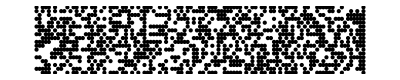

```mathematica
f[x_,y_]:= Floor[Mod[Floor[y/17]*2^(-17*Floor[x]-Mod[Floor[y],17]),2]]
n = 4858450636189713423582095962494202044581400587983244549483093085061934704708809928450644769865524364849997247024915119110411605739177407856919754326571855442057210445735883681829823754139634338225199452191651284348332905131193199935241375876523926487461339490687013056229581321948111368533953556529085002387509285689269455597428154638651073004910672305893358605254409666435126534936364395712556569593681518433485760526694016125126695142155053955451915378545752576590740540157929001765967965480064427829131488548259914721248506352686630476300
points = {}
For[x=0,x<107,x++,For[y=n,y<n+18,y++,If[f[x,y]<1/2,AppendTo[points,{x,y-n}]]]]
Graphics[Point[points]]
```